## Quick Start: Basic Concepts and Syntax

## Learning Objectives

### The Basics

Two main parts of the Wolfram System: front end and kernel

Data's round trip and session history

The notebook as a structured computable document

Using built-in functions

Finding help from the documentation

### Coding in Notebooks

Helpful features of the notebook interface

Input assistance

Wolfram Language syntax

Shortcuts and menu items

### Symbolic Expressions

Structure of an expression

Meaning of an expression

Components of an expression

Parts of an expression

Expressions as trees

Accessing a part of an expression

Levels in expressions

## Front End and Kernel

Two main parts of the Wolfram System are:

Wolfram Language kernel (performs computations)

The Wolfram System front end (handles interactions with the user)

The most common way to work on the Wolfram System (desktop and cloud) is to use the interactive Wolfram Notebook (part of the front end).

### Your Data's Round Trip

The following outlines the interaction between the front end and the kernel during a computation:

When you enter a Wolfram Language input into a notebook and press Shift+Enter, the front end parses your input into a FullForm expression and passes it to the kernel.

The kernel evaluates the expression and returns the result to the front end as a FullForm expression.

The front end renders the result in an appropriate manner in your notebook, and subsequently an output cell is generated.

```mathematica
2+2
```

4

The kernel may be run either on the same computer as the front end or on another computer connected via a network. Sometimes, the kernel is not even started until you actually do some computation with Wolfram Language.

### Wolfram System Session History

Each input and output cell is indexed by a number n, (seen in the labels In[n] or Out[n] to the left of the cells). The number n refers to the sequence of the evaluation in the current session.

Previously evaluated inputs and their corresponding outputs are stored symbolically in a sequence of In and Out objects.

In[n] causes the n^th input line to be reevaluated.

Out[n] returns the n^th output expression.

```mathematica
3+4
```

7

```mathematica
In[12]
```

4

```mathematica
Out[12]
```

4

The last result generated can also be accessed using %:

%% gives the second-to-last result.

%%...% (k times) gives the k^th previous result.

%n gives the result from Out[n].

```mathematica
5^2
%+25
%%+225
%%+1000
```

## The Notebook

Wolfram Notebooks provide:

A complete high-level programmatic interface

An environment to build arbitrary dynamic interfaces

Familiar word-processing metaphors to create full, typeset, publishable documents

### Cells

A notebook is a structured document:

The structure is delineated by the "cell." A notebook consists of a hierarchical collection of cells.

Cells typically have distinct brackets on the right.

#### Inserting, editing and selecting cells

The cell insertion bar is a solid gray line with a small black cursor running horizontally across the notebook that appears when you click within the blank section of a notebook or between cells. The cell insertion bar is the place where new cells will be created.

The cursor is a vertical bar that appears when hovering over a cell. Clicking there allows creation, modification or deletion of content.

The cell selector is a left arrow ⇤ that appears when hovering over the cell brackets. Clicking there allows selection of whole cells for copying, cutting, deleting or setting properties.

#### Cell styles

A cell may contain narrative text, code, math, images or some combination. The type of content is dictated by the style of the cell:

The default style of a cell is "Input", meaning Wolfram Language input.

You can select the style from the "+" icon on the cell insertion bar or from the menu Format ▶ Style.

You can use shortcut keys to set the style: Alt7 or Cmd7 for Text, Alt4 or Cmd4 for Section, Alt5 or Cmd5 and so on.

You can change the style of an existing cell by selecting the cell bracket and then selecting the new style from the Format menu or using shortcut keys.

### Notebooks Are Computable

In Wolfram Language's unified symbolic architecture, every Wolfram Language notebook you see is represented as a symbolic expression that can be manipulated and controlled programmatically using Wolfram Language:

The notebook document is represented as a Notebook expression by the front end.

It is written to the storage device as an expression. It can be, and sometimes is, read as data! (Take a peek with TextEdit or Notepad.)

There are special comments included that allow the front end to handle the file efficiently. Therefore, it is best to edit the file only with the Wolfram System front end.

Notebooks can be created programmatically:

```mathematica
NotebookPut[Notebook[{Cell["Section heading","Section"],Cell["Some text.","Text"],Cell["More text.","Text"]}]]
```

3170d86b-54b4-495a-aed6-3de290b1cf7eUntitled-1

The raw expression corresponding to a notebook can be read in from the NotebookObject:

```mathematica
NotebookGet[%]
```

Notebook[{Cell[CellGroupData[{Cell[head,Section],Cell[text,Text]},Open]]},WindowSize→{808,755},WindowMargins→{{316,Automatic},{Automatic,50}},FrontEndVersion→12.3 for Mac OS X x86 (64-bit) (May 11, 2021),StyleDefinitions→Default.nb]

It is possible to extract the contents from a notebook with code:

```mathematica
NotebookImport[EvaluationNotebook[],"Section"]
```

## Built-in Functions

There are 6400+ built-in functions in Wolfram Language:

All built-in functions use square brackets to accept their arguments and have names that start with Capital letters.

The names of built-in functions are complete English words or—in some cases—standard mathematical abbreviations. American spelling is used.

```mathematica
Range[10]
```

```mathematica
RandomInteger[10]
```

```mathematica
RandomWord[]
```

Functions whose names end with Q usually "ask a question," and evaluate to either True or False.

```mathematica
EvenQ[4]
```

```mathematica
PrimeQ[37]
```

The context-sensitive autocompletion menu displays a list of possible functions as you type.

Similar functions take similarly structured input and produce similarly structured output.

A group of functions that perform tasks having a common theme are often named similarly.

```mathematica
-Graphics--Graphics-
```

The notion of a function is considerably more general in Wolfram Language than in either traditional mathematics or computer science. For example, f[anything] is considered a function, whether it evaluates to something definite or remains in symbolic form.

### Wolfram Function Repository

In the case that you cannot find a function that does exactly what you want, you should take a quick look at the Wolfram Function Repository. Many useful functions that are perhaps a little too specific for general inclusion in Wolfram Language find their home here, contributed both by Wolfram employees and enthusiasts and vetted by a dedicated team.

Repository functions span many different topic areas. Here are a few of these functions:

```mathematica
ResourceFunction["ColorToHex"][Pink]
```

#ff8080

```mathematica
ResourceFunction["XKCDConvert"][BarChart[{10,1},ChartLabels->{"XKCD","Others"},]]
```

-Graphics-

```mathematica
ResourceFunction["AddIndices"][{a,b,c,d}]
```

{{1,a},{2,b},{3,c},{4,d}}

```mathematica
With[{v={0,1,2}},basis=ResourceFunction["BasisFromVector"][v]]
```

{{0,1/(√5),2/(√5)},{1,0,0},{0,1-1/(5 (1+2/(√5))),-1/(√5)}}

Some of these functions see enough usage that they are eventually integrated into the language itself (e.g. PositionLargest and PositionSmallest). If you come up with a function that you think other people might find useful, you can easily submit your own right from your Mathematica installation (File ▶ New ▶ Repository Item ▶ Function Repository Item).

## Documentation

Detailed documentation on all Wolfram Language functionality can be accessed from Help ▶ Wolfram Documentation.

For the documentation on a particular function, hover over the function name and click the "i":

A summary of information available from the documentation page:

Basic usage of the function

Additional usage of the function (that may not be obvious)

Various options available for customizing the function

Examples showing how the option values can be set

Examples showing basic use of the function as well as advanced applications

Lists of related functions along with links to their documentation pages

Links to "guide pages" (collections of functions in a specific category or field of application) where the function is mentioned, so you can explore other functions from the same area

Links to tutorials and workflows

## Coding in Notebooks

### Input Assistance

Some features can help you recognize the structure and identify possible issues with code:

Undefined symbol names show up in blue but change color to black when defined.

```mathematica
Fra
```

```mathematica
Framed
```

```mathematica
Framed[abc]
```

```mathematica
abc = 2
```

Syntax coloring provides hints about the scope of certain symbols.

```mathematica
add[a_,b_]:=a+b
```

```mathematica
Table[n^2,{n,4}]
```

```mathematica
#^2+#+1&
```

```mathematica
{1,2,3,4,5}/.n_Integer/;PrimeQ[n]:>n^2
```

Built-in and user-defined symbols are automatically suggested while typing.

Dynamic highlighting adds emphasis to the current function name as well as any matching brackets, braces and parentheses and specifies "where you are" inside complex expressions.

Triple-clicking establishes useful structured selections in code. Try triple-clicking at various positions below.

```mathematica
TabView[Table[Framed[Plot3D[n*Cos[x y], {x, 0, 2π},{y,0,2π}]],{n,1,6,1}]]
```

### Wolfram Language Syntax

#### The usual suspects

Some of the more familiar components of the rich syntax of Wolfram Language:

Strings

```mathematica
"Hello"
```

Integers and real numbers

```mathematica
1
```

```mathematica
1.23
```

Operators

```mathematica
+
```

```mathematica
>
```

```mathematica
&&
```

Symbols: defined or undefined (Wolfram Language is fully symbolic, so "undefined variables" can always just stand for themselves)

```mathematica
Pi
```

```mathematica
x
```

```mathematica
α
```

Wolfram Language symbols are the ultimate atoms of symbolic data. Every symbol has a unique name, exists in a certain Wolfram Language context or namespace and can have a variety of types of values and attributes.

#### Brackets

Four kinds of brackets are used in Wolfram Language, each serving a different purpose:

Square brackets for functions

```mathematica
RandomInteger[]
```

Curly braces for lists

```mathematica
{1,2,3,4,5}
```

Double square brackets for indexing

```mathematica
myList={1,2,3,4,5}; 
	myList[[3]]
```

Parentheses for grouping operations

```mathematica
(a+b)/c
```

#### Precedence of operators

The usual rules of algebra apply for precedence of operators:

exponentiation > {multiplication
division > {addition
subtraction > negation

All operators (e.g. ⊗) have a precedence assigned to them

Parentheses should be used for explicitly grouping terms (never curly braces or square brackets)

```mathematica
2+3*5
```

17

```mathematica
(2+3)*5
```

25

#### Special notations for functions

Wolfram Language offers a few short forms for function applications:

Standard function application

```mathematica
Reverse[{1,2,3,4,5}]
```

```mathematica
Join[{1,2},{3,4}]
```

Prefix function application

```mathematica
Reverse@{1,2,3,4,5}
```

Postfix function application

```mathematica
{1,2,3,4} //Reverse
```

Infix function application

```mathematica
{1,2}~Join~{3,4}
```

#### Comment

Comments can be included in your code as follows:

```mathematica
(*Ignore this*)
```

#### Iconize

You can apply Iconize to any part of an input that is too large or not sufficiently relevant. The iconized expression is an exact stand-in for the original input:

```mathematica
Iconize[RandomReal[{0,1},500],"Random List"]
```

While you can manually iconize some expression by using the function, it is more common to highlight some portion of an input and choose "Un/Iconize Selection" from the context menu:

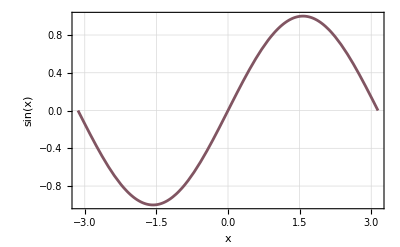

```mathematica
Plot[Sin[x],{x,-π,π},]
```

#### Suppress output

Adding a semicolon at the end of an input suppresses the output:

```mathematica
myList = RandomInteger[10,{100,2}];
```

The semicolon is actually infix for CompoundExpression:

```mathematica
a=1;b=2;c=3;
```

If you end your input with a semicolon, it is as if you are giving a sequence of operations with an "empty" one at the end.

### Shortcuts and Menu Items

The following keyboard shortcuts can be useful while working in notebooks:

Ctrl+L: Copy input from above

Shift+Ctrl+L: Copy output from above

Cmd+Shift+K (or Ctrl+Shift+K) after typing in a function name: Brings up a list of function templates

Ctrl+Shift+': Un/Iconize selection

You can evaluate all the cells in a notebook at once from the menu using Evaluation ▶ Evaluate Notebook.

## Symbolic Expressions

Everything in Wolfram Language is a symbolic expression. Sometimes expressions look similar; sometimes they look very different.

A prototypical example of a Wolfram Language expression is:

f[x,y,z,...]

### Structure of an Expression

Most expressions look similar:

They begin with a word that starts with a capital letter.

They have square brackets.

Elements enclosed in the square brackets are separated from one another using commas.

Sometimes there are no elements within the square brackets.

```mathematica
StringJoin["Hello","World"]
```

```mathematica
Classify["Language","the house is blue"]
```

```mathematica
ConstantArray[c,10]
```

```mathematica
Graphics[{Red,Disk[],Green,Rectangle[{0,0},{2,2}],Blue,Disk[{2,2}]}]
```

```mathematica
DateString[]
```

You will also run into expressions that look nothing like the template shown:

```mathematica
a+b
```

```mathematica
a+b^2+Sin[3*c^3]
```

```mathematica
{x,y,z}
```

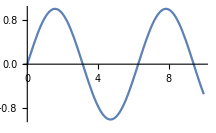

The true underlying structure can be revealed with the FullForm function:

```mathematica
FullForm[a+b]
```

```mathematica
FullForm[a+b^2+Sin[3*c^3]]
```

```mathematica
FullForm[{x,y,z}]
```

```mathematica
FullForm[-Graphics3D-]
```

```mathematica
FullForm[Entity["City",{"Champaign","Illinois","UnitedStates"}]]
```

You can use Head to see the head of any expression:

```mathematica
(-b+√(b^2-4a c))/(2a)
```

```mathematica
Head[(-b+√(b^2-4a c))/(2a)]
```

```mathematica
FullForm[ (-b+√(b^2-4a c))/(2a)]
```

```mathematica
Head[{x,y,z}]
```

```mathematica
Head[-Graphics3D-]
```

```mathematica
Head[Entity["City",{"Champaign","Illinois","UnitedStates"}]]
```

### Meaning of an Expression

In an expression f[x,y,...], f can be interpreted as:

a function or command with x and y as arguments or parameters

```mathematica
Sin[x]
```

```mathematica
EdgeDetect[-Graphics3D-]
```

a type of object with x and y as its contents

```mathematica
RGBColor[1,0,0]
```

```mathematica
Entity["City",{"Champaign","Illinois","UnitedStates"}]
```

an operator with x and y as operands

```mathematica
x+y
```

```mathematica
Plus[x,y]
```

a head with x and y as elements

```mathematica
{x,y,z}
```

```mathematica
List[x,y,z]
```

### Components of an Expression

#### Atomic expressions

All expressions in Wolfram Language are ultimately built from a small number of distinct types of atomic elements:

Numbers: Integer, Rational, Real, Complex and other representation of numbers

```mathematica
127
```

```mathematica
3/4
```

```mathematica
0.0004
```

```mathematica
5+3I
```

String: anything enclosed in double quotes

```mathematica
"String"
```

```mathematica
"123"
```

Symbol: a concatenation of characters not beginning with a number

```mathematica
symbol
```

```mathematica
variable
```

```mathematica
x
```

Symbols are the basic named objects in Wolfram Language. Every symbol has a unique name.

The name:

consists of a concatenation of letters, numbers and other characters

cannot begin with a number

cannot begin with or contain certain reserved special characters (e.g. !, @, #, %, ^, +, -, _, =, &, (, ), {, }, [, ], etc.)

Syntax coloring changes from Blue to Black when a symbol name is recognized.

Atomic expressions have a head as well:

```mathematica
Head[3]
```

```mathematica
Head[3.1415926]
```

```mathematica
Head[3-2ⅈ]
```

```mathematica
Head[Pi]
```

```mathematica
Head["pie"]
```

You can check whether an expression is an atom or not using AtomQ:

```mathematica
AtomQ[3]
```

```mathematica
AtomQ[3.1415926]
```

```mathematica
AtomQ[3-2ⅈ]
```

```mathematica
AtomQ[Pi]
```

```mathematica
AtomQ["pie"]
```

#### Composite expressions

Atomic expressions can be combined to build up composite expressions. You can also nest composite expressions to build progressively more complicated expressions.

Here is a composite expression built up from multiple atomic elements:

```mathematica
Times[Rational[1,2],Power[a,-1],Plus[Times[-1,b],Power[Plus[Power[b,2],Times[-4,a,c]],Rational[1,2]]]]
```

## Parts of an Expression

### Expressions as Trees

You can think of any Wolfram Language expression as a tree.

Here is an expression in full form:

```mathematica
FullForm[(-b+√(b^2-4a c))/(2a)]
```

TreeForm prints out expressions to show their "tree" structure:

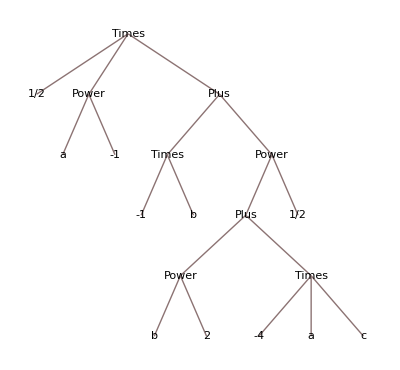

```mathematica
TreeForm[(-b+√(b^2-4a c))/(2a)]
```

### Accessing a Part of an Expression

Now that you have visualized expressions built out of many parts, you can think of working with these parts individually or in combination.

You can use Part to extract any part of an expression:

```mathematica
Part[x+y+z,2]
```

y

```mathematica
Part[(-b+√(b^2-4a c))/(2a),2]
```

```mathematica
Part[(-b+√(b^2-4a c))/(2a),3,1]
```

-b

```mathematica
Part[(-b+√(b^2-4a c))/(2a),3,2]
```

√(b^2-4 a c)

### Levels in Expressions

When your expressions have fairly uniform structure, it is often convenient to be able to refer to a whole collection of parts at the same time.

Levels provide a general way of specifying collections of parts in Wolfram Language expressions with nested elements.

Here is the expression tree:

```mathematica
TreeForm[(-b+√(b^2-4a c))/(2a)]
```

-Graphics-

Show the elements at different levels:

```mathematica
Level[(-b+√(b^2-4a c))/(2a),{1}]
```

{1/2,1/a,-b+√(b^2-4 a c)}

```mathematica
Level[(-b+√(b^2-4a c))/(2a),{2}]
```

{a,-1,-b,√(b^2-4 a c)}

```mathematica
Level[(-b+√(b^2-4a c))/(2a),{3}]
```

{-1,b,b^2-4 a c,1/2}

```mathematica
Level[(-b+√(b^2-4a c))/(2a),3]
```

{1/2,a,-1,1/a,-1,b,-b,b^2-4 a c,1/2,√(b^2-4 a c),-b+√(b^2-4 a c)}

## References

The Structure of the Wolfram System

Using a Notebook Interface

Managing Computations in Notebooks

The Syntax of the Wolfram Language

Some General Notations and Conventions

Basic Objects

Expressions